Settings (phi = 0.0 rad):  tA=0.000 ps,  tB=1.552 ps,  tA'=3.104 ps,  tB'=10.865 ps  (T=12.417 ps)

GammaH=0.667 ps^-1,  GammaL=0.667 ps^-1,  ΔΓ=0.000 ps^-1,  C=1.

Window half-width sigmaWin = 0.3 ps

Selected counts:  AB=25600   A'B=7325   AB'=45   A'B'=15

Total pairs selected (across all four settings) = 32985

--- CHSH (empirical, decaying state) ---

E(AB)=-303/400  E(A'B)=-5193/7325  E(AB')=-11/15  E(A'B')=11/15

S_empirical = -2.933

--- CHSH (theory, averaging exact times of selected pairs) ---

S_theory_from_selected_pairs = S_fromPairs

S_theory_at_markers = S_markers  (max |S| ≤ 2.828 at this geometry)

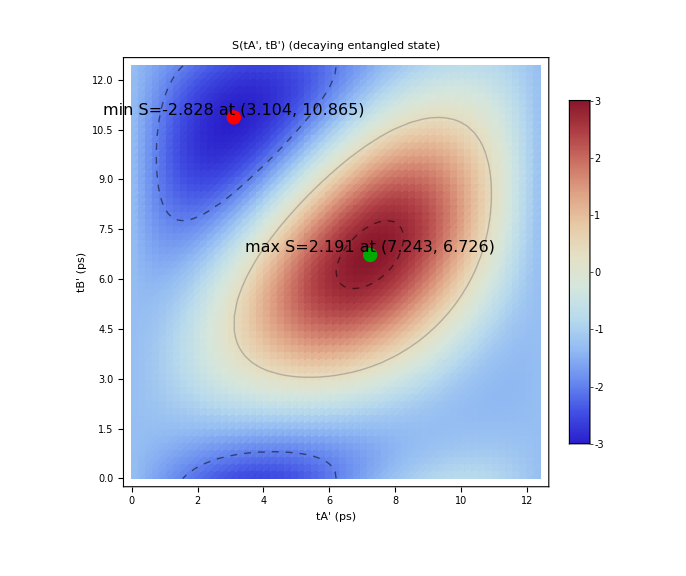

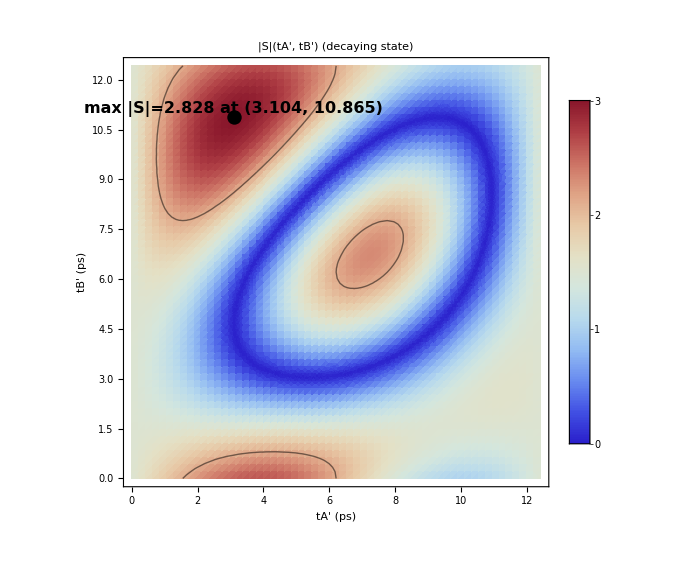

Max S = 2.191 at  tA'=7.243 ps,  tB'=6.726 ps

Min S = -2.828 at  tA'=3.104 ps,  tB'=10.865 ps

Max |S| = 2.828 at  tA'=3.104 ps,  tB'=10.865 ps

```mathematica
ClearAll["Global`*"];

(*For texts*)
fsTick=16;  
fsLabel=18;  
fsTitle=20;  
fsInset=16;  

$TextStyle={FontFamily->"Helvetica"};

(*Mixing& decay parameters*)
deltaM=0.506;                 (*ps^-1*)
tauAvg=1.5;                   (*mean lifetime~1/GammaAvg,ps*)
GammaAvg=1/tauAvg;              (*ps^-1*)
dGamma=0.0;                   (*ΔΓ=Γ_H-Γ_L (ps^-1);set>0 if needed*)
GammaH=GammaAvg+dGamma/2;   (*ps^-1*)
GammaL=GammaAvg-dGamma/2;   (*ps^-1*)
Cmix=1.0;                   (*C= |p|^2/|q|^2;C=1->CP conservation*)

T=2 Pi/deltaM;                  (*oscillation period (ps)*)

(*Time-selection window& ensemble*)
sigmaWin=0.3;                   (*ps,half-window*)
nPairs=1000000;               (*ensemble size*)

(*CHSH-optimal time markers*)
phi=0.;
tWrap[t_]:=Mod[t,T];
tA=tWrap[phi/deltaM];
tB=tWrap[(phi+Pi/4)/deltaM];
tAp=tWrap[(phi+Pi/2)/deltaM];
tBp=tWrap[(phi-Pi/4)/deltaM];

(* Decaying entangled state:F and E(t1,t2)*)
Fdec[t1_,t2_]:=Cos[deltaM (t1-t2)]/Cosh[dGamma (t1-t2)/2];
Dden[F_]:=(Cmix+1)^2-(Cmix-1)^2 F;
Edec[t1_,t2_]:=((Cmix-1)^2-(Cmix+1)^2 Fdec[t1,t2])/Dden[Fdec[t1,t2]];

(*CHSH from arbitrary markers*)
Smarkers[tA_,tAp_,tB_,tBp_]:=Edec[tA,tB]+Edec[tAp,tB]+Edec[tA,tBp]-Edec[tAp,tBp];

(*  Ensemble of meson pairs with proper H/L widths*)
SeedRandom[20250828];

expSample[gamma_]:=-Log[1-RandomReal[]]/gamma;

(*produce (tL,tR) from mixture e^{-Γ_L tL-Γ_H tR}+e^{-Γ_H tL-Γ_L tR}*)
pairs=Table[If[RandomReal[]<1/2,<|"id"->i,"tL"->expSample[GammaL],"tR"->expSample[GammaH]|>,<|"id"->i,"tL"->expSample[GammaH],"tR"->expSample[GammaL]|>],{i,nPairs}];

Print["Settings (phi = ",NumberForm[phi,{3,1}]," rad):  tA=",NumberForm[tA,{5,3}]," ps,  tB=",NumberForm[tB,{5,3}]," ps,  tA'=",NumberForm[tAp,{5,3}]," ps,  tB'=",NumberForm[tBp,{5,3}]," ps  (T=",NumberForm[T,{5,3}]," ps)"];

Print["GammaH=",NumberForm[GammaH,{4,3}]," ps^-1,  GammaL=",NumberForm[GammaL,{4,3}]," ps^-1,  ΔΓ=",NumberForm[dGamma,{4,3}]," ps^-1,  C=",Cmix];

Print["Window half-width sigmaWin = ",sigmaWin," ps"];

(*To select pairs that fall in any of the four setting windows*)
within[t_,c_]:=Abs[t-c]<=sigmaWin;
combos={{"AB",tA,tB},{"ApB",tAp,tB},{"ABp",tA,tBp},{"ApBp",tAp,tBp}};
buckets=<|"AB"->{},"ApB"->{},"ABp"->{},"ApBp"->{}|>;

Scan[Function[p,Module[{tL=p["tL"],tR=p["tR"],matches,best},matches=Select[combos,within[tL,#[[2]]]&&within[tR,#[[3]]]&];
If[matches=!={},best=First@SortBy[matches,Abs[tL-#[[2]]]+Abs[tR-#[[3]]]&];
buckets[best[[1]]]=Append[buckets[best[[1]]],{tL,tR}];];]],pairs];

qAB=Length[buckets["AB"]];
qApB=Length[buckets["ApB"]];
qABp=Length[buckets["ABp"]];
qApBp=Length[buckets["ApBp"]];
totalSelected=qAB+qApB+qABp+qApBp;

Print["Selected counts:  AB=",qAB,"   A'B=",qApB,"   AB'=",qABp,"   A'B'=",qApBp];
Print["Total pairs selected (across all four settings) = ",totalSelected];

(* CHSH from these pairs (decaying state)*)

(*draw {s1,s2}∈{±1}^2 from the conditional probabilities at (t1,t2)*)
sampleOutcomeDecaying[t1_,t2_]:=Module[{F=Fdec[t1,t2],D,pPP,pPm,pmP,pmm},D=Dden[F];
pPP=Cmix^2 (1-F)/D;(*{+1,+1}*)pPm=Cmix (1+F)/D;(*{+1,-1}*)pmP=Cmix (1+F)/D;(*{-1,+1}*)pmm=(1-F)/D;(*{-1,-1}*)RandomChoice[{pPP,pPm,pmP,pmm}->{{1,1},{1,-1},{-1,1},{-1,-1}}]];

empiricalE[plist_List]:=If[Length[plist]==0,Missing["NoData"],Mean@(Times@@@(sampleOutcomeDecaying[#[[1]],#[[2]]]&/@plist))];

theoryE[plist_List]:=If[Length[plist]==0,Missing["NoData"],Mean@(Edec[#[[1]],#[[2]]]&/@plist)];

EABemp=empiricalE[buckets["AB"]];
EApBemp=empiricalE[buckets["ApB"]];
EABpemp=empiricalE[buckets["ABp"]];
EApBpemp=empiricalE[buckets["ApBp"]];

EABth=theoryE[buckets["AB"]];
EApBth=theoryE[buckets["ApB"]];
EABpth=theoryE[buckets["ABp"]];
EApBpth=theoryE[buckets["ApBp"]];

haveEmp=VectorQ[{EABemp,EApBemp,EABpemp,EApBpemp},NumericQ];
haveTh=VectorQ[{EABth,EApBth,EABpth,EApBpth},NumericQ];

If[haveEmp,Semp=N[EABemp+EApBemp+EABpemp-EApBpemp,6];
Print["--- CHSH (empirical, decaying state) ---"];
Print["E(AB)=",NumberForm[EABemp,{5,3}],"  E(A'B)=",NumberForm[EApBemp,{5,3}],"  E(AB')=",NumberForm[EABpemp,{5,3}],"  E(A'B')=",NumberForm[EApBpemp,{5,3}]];
Print["S_empirical = ",NumberForm[Semp,{6,3}]],Print["Not enough data in one or more buckets to form S_empirical."]];

If[haveTh,S_fromPairs=N[EABth+EApBth+EABpth-EApBpth,6];
Print["--- CHSH (theory, averaging exact times of selected pairs) ---"];
Print["S_theory_from_selected_pairs = ",NumberForm[S_fromPairs,{6,3}]],Print["Not enough data in one or more buckets to form S_theory_from_selected_pairs."]];

(*Ideal S at the nominal markers*)
S_markers=N[Smarkers[tA,tAp,tB,tBp],10];
Print["S_theory_at_markers = ",NumberForm[S_markers,{6,4}],"  (max |S| ≤ 2.828 at this geometry)"];

(* 2D visualisations *)

sRange={0,T};
constraints=sRange[[1]]<=u<=sRange[[2]]&&sRange[[1]]<=v<=sRange[[2]];

maxData=NMaximize[{Smarkers[tA,u,tB,v],constraints},{u,v}];
minData=NMinimize[{Smarkers[tA,u,tB,v],constraints},{u,v}];
absData=NMaximize[{Abs[Smarkers[tA,u,tB,v]],constraints},{u,v}];

maxS=maxData[[1]];{uMax,vMax}={u,v}/. maxData[[2]];
minS=minData[[1]];{uMin,vMin}={u,v}/. minData[[2]];
maxAbsS=absData[[1]];{uAbs,vAbs}={u,v}/. absData[[2]];

(*Heatmap of S*)
heatS=DensityPlot[Smarkers[tA,u,tB,v],{u,sRange[[1]],sRange[[2]]},{v,sRange[[1]],sRange[[2]]},PlotRange->{-3,3},PlotPoints->60,MaxRecursion->2,ColorFunction->"ThermometerColors",ColorFunctionScaling->True,Frame->True,AspectRatio->1,FrameLabel->(Style[#,fsLabel]&/@{"tA' (ps)","tB' (ps)"}),LabelStyle->Directive[fsLabel],FrameTicksStyle->Directive[fsTick],PlotLabel->Style["S(tA', tB')  (decaying entangled state)",fsTitle,Bold],ImageSize->Large,PerformanceGoal->"Quality"];

contoursS=ContourPlot[Smarkers[tA,u,tB,v],{u,sRange[[1]],sRange[[2]]},{v,sRange[[1]],sRange[[2]]},Contours->{-2,0,2},ContourStyle->{Directive[Thick,Dashed],Directive[Thick,GrayLevel[.5]],Directive[Thick,Dashed]},ContourShading->False,Frame->False,AspectRatio->1,LabelStyle->Directive[fsLabel],FrameTicksStyle->Directive[fsTick],PerformanceGoal->"Quality"];

annS=Graphics[{Darker[Green],PointSize[0.018],Point[{uMax,vMax}],Black,Inset[Style[Row[{"max S=",NumberForm[maxS,{5,3}]," at (",NumberForm[uMax,{5,3}],", ",NumberForm[vMax,{5,3}],")"}],fsInset],{uMax,vMax},{0,-1.5}],Red,PointSize[0.018],Point[{uMin,vMin}],Black,Inset[Style[Row[{"min S=",NumberForm[minS,{5,3}]," at (",NumberForm[uMin,{5,3}],", ",NumberForm[vMin,{5,3}],")"}],fsInset],{uMin,vMin},{0,-1.5}]}];


legendS=BarLegend[{"ThermometerColors",{-3,3}},Ticks->Range[-3,3],LegendLabel->None,LabelStyle->Directive[fsTick],TicksStyle->Directive[fsTick],LegendMarkerSize->{Automatic,260}];

plotS=Legended[Show[heatS,contoursS,annS,ImageSize->Large],Placed[legendS,Right]];

Print@plotS;

(*Heatmap of|S|*)
heatAbs=DensityPlot[Abs[Smarkers[tA,u,tB,v]],{u,sRange[[1]],sRange[[2]]},{v,sRange[[1]],sRange[[2]]},PlotRange->{0,3},PlotPoints->60,MaxRecursion->2,ColorFunction->"ThermometerColors",ColorFunctionScaling->True,Frame->True,AspectRatio->1,FrameLabel->(Style[#,fsLabel]&/@{"tA' (ps)","tB' (ps)"}),LabelStyle->Directive[fsLabel],FrameTicksStyle->Directive[fsTick],PlotLabel->Style["|S|(tA', tB')  (decaying state)",fsTitle,Bold],ImageSize->Large,PerformanceGoal->"Quality"];

contoursAbs=ContourPlot[Abs[Smarkers[tA,u,tB,v]],{u,sRange[[1]],sRange[[2]]},{v,sRange[[1]],sRange[[2]]},Contours->{2},ContourStyle->{Directive[Thick,Black]},ContourShading->False,Frame->False,AspectRatio->1,LabelStyle->Directive[fsLabel],FrameTicksStyle->Directive[fsTick],PerformanceGoal->"Quality"];

annAbs=Graphics[{Black,PointSize[0.018],Point[{uAbs,vAbs}],Black,Inset[Style[Row[{"max |S|=",NumberForm[maxAbsS,{5,3}]," at (",NumberForm[uAbs,{5,3}],", ",NumberForm[vAbs,{5,3}],")"}],fsInset,Bold],{uAbs,vAbs},{0,-1.5}]}];


legendAbs=BarLegend[{"ThermometerColors",{0,3}},Ticks->Range[0,3],LegendLabel->None,LabelStyle->Directive[fsTick],TicksStyle->Directive[fsTick],LegendMarkerSize->{Automatic,260}];

plotAbs=Legended[Show[heatAbs,contoursAbs,annAbs,ImageSize->Large],Placed[legendAbs,Right]];

Print@plotAbs;

Print["Max S = ",NumberForm[maxS,{6,3}]," at  tA'=",NumberForm[uMax,{5,3}]," ps,  tB'=",NumberForm[vMax,{5,3}]," ps"];
Print["Min S = ",NumberForm[minS,{6,3}]," at  tA'=",NumberForm[uMin,{5,3}]," ps,  tB'=",NumberForm[vMin,{5,3}]," ps"];
Print["Max |S| = ",NumberForm[maxAbsS,{6,3}]," at  tA'=",NumberForm[uAbs,{5,3}]," ps,  tB'=",NumberForm[vAbs,{5,3}]," ps"];
```